### Similar sizing --Willem

-Graphics-

```mathematica
GraphicsRow[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},150,ImageSize->{Automatic, 260},"Decay"->.7],
CellularAutomatonPlot3D["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},100,ImageSize->{Automatic, 262},ViewPoint->{3.0373115164062576,-1.449486231706877,0.35175050305311767}(*, ImageSize-> {75, Automatic}*)],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->{Automatic, 260},Mesh->None]}(*,Spacer[0]*)]
```

-Graphics-

### Use ColorData[“DefaultPlotColors”]

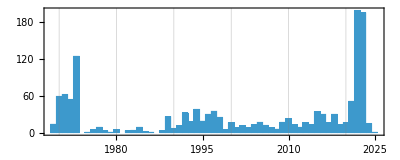

```mathematica
Histogram[Values[#Year&/@$LifeData],{1},Frame->True,AspectRatio->.4,FrameLabel->{"year",None},GridLines->{Range[1970,2020,10],None}, ChartStyle->ColorData[116, "ColorList"][[1]]]
```

Changed code:

```mathematica
Histogram[Values[#Year&/@$LifeData],{1},Frame->True,AspectRatio->.4,FrameLabel->{"year",None},GridLines->{Range[1970,2020,10],None}, ChartStyle->ColorData["DefaultPlotColors", "ColorList"][[1]]]
```

-Graphics-

### Use ColorData[“DefaultPlotColors”]

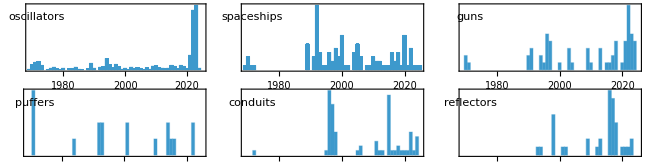

```mathematica
GraphicsGrid[Partition[KeyValueMap[Histogram[#2,{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},AspectRatio->.3,ImageSize->200,PlotRangePadding->{Automatic,{0,Scaled[.15]}},Epilog->Style[Text[ToLowerCase[Pluralize@#1],Scaled[{.06,.8}],{-1,0}],11],
ChartStyle->ColorData["DefaultPlotColors", "ColorList"][[1]]]&,],3],ImageSize->650,Spacings->{3,7}]
```

### Make bars narrower

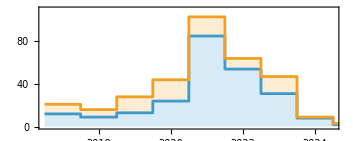

```mathematica
ListStepPlot[Reverse/@Transpose[Most[{Total@Sign@StringCount[#,"discover"|"use"],Total@Sign@StringCount[#,"construct"]}&/@ydata]],Center,PlotLayout->"Stacked",Filling->{2->{1},1->Axis},Frame->True,PlotRange->{{0.5,8.5},{0,110}},PlotLegends->{"search","construction"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Transpose[{Range[2,8],Riffle[Range[2018,2024,2],None]}],Automatic}}]
```

This is wrong^^^ the first bit of data is not 2017 it’s 2009!!!!

```mathematica
(*CORRECT: see WN-31-Ydata for iys retrieval (it was a fricking nightmare)*)
```

Design needs to fix colors

```mathematica
iys = ;
```

```mathematica
counts = {StringCount[#,"discover"|"use"],StringCount[#,"construct"]}&/@ Most@*Reverse@*Most@iys;
```

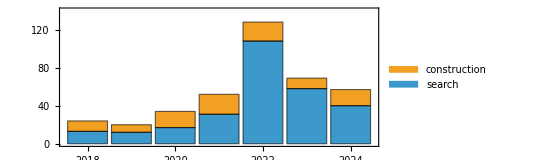

```mathematica
BarChart[counts, ChartLayout->"Stacked",PlotRange->{{0.5,7.5},{0,140}},ChartLegends->{"search","construction"},AspectRatio->.4,Frame->True, FrameTicks->{{Automatic,None},{Transpose[{Range[1,7],Riffle[Range[2018,2025,2],None]}],Automatic}}, ChartStyle->{ColorData["DefaultPlotColors"][1], ColorData["DefaultPlotColors"][2]}, BarSpacing->.1]
```

### Add pattern callout. Possibly add horizontal guides.

But after that, for nearly two decades, no more spaceships were found.  In 1989, however, a systematic method for searching was invented, and in the years since, a steady stream of new spaceships have been found.  A variety of different periods have been seen

Add pattern callout
Possibly add horizontal guides

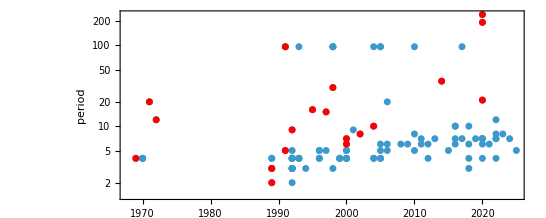

```mathematica
With[{data=Values[{#Year,#Period}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log"]]
```

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1,Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[RGBColor[0.24, 0.6, 0.8], PointSize[.01]], PlotRangePadding->{ {Automatic, 0}, Automatic}]
```

-Graphics-

Not right, bit of a challenge with the log scaling

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1,Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> RGBColor[0.24, 0.6, 0.8],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&])[[All, -1]]})

]
```

-Graphics-

### Fix munging

For Developer

```mathematica
oprimitives=Select[Keys[Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],IsPrimitive[Normal[$LifeData[#]["MatrixData"]]]&];
```

```mathematica
alloprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{PatternCanonicalize2[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[$LifeData[#]])&,oprimitives]];
```

```mathematica
oresall=Association[DeleteCases[ParallelMap[#->MemoryConstrained[(PatternCheck[#,alloprims]&/@CanonicalParts[Normal[$LifeData[#]["MatrixData"]]]),10^7]&,Keys[Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]],x_->{x_}]];
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,GraphicsColumn[{ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[100],100}],$LifeData[#1]["Period"]}]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

```mathematica
oresall = ;
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,
ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[125],125}, Mesh->True,MeshStyle->Opacity[.1], Epilog->{FaceForm@Transparent, Rectangle[Scaled[{0, .25}], Scaled[{1, 1}]],Style[Text[$LifeData[#1]["Period"], Scaled[{.5,.25}]], 9]}, PlotRangePadding->{Automatic, Scaled/@{.45, 0}}, Frame->False]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

### Fix x’s Align images at the top

This is correct:

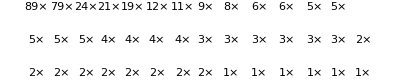

```mathematica
GraphicsGrid[
Function[row, Take[row, #]&/@ {{1, 13}, {14, 27}, {28, -1}}][KeyValueMap[Labeled[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.2],ImageSize->{Automatic, 30}],Text[Style[StringTemplate["``×"][#2], 11]],Top]&,ReverseSort@PatternElements[SparseArray[…]]]](*, Spacings->{12, Automatic}*)]
```

### Remove 0 from y scale

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]],PlotRange->{1, 30},Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

### PM: from Willem below SW wanted labels below:

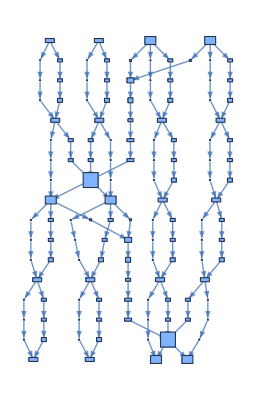
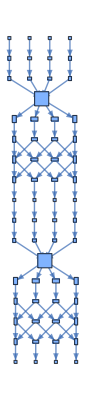
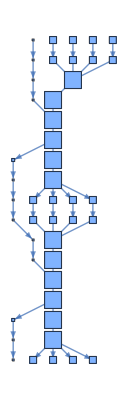
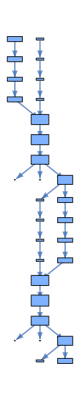
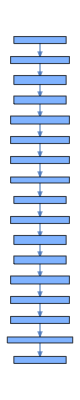
1983 | 1994 | 1994 | 2016 | 2020
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
Grid[{
Style[Text[#Year], 11]&/@SortBy[allimps[[15]],#Year&],
Column[{
BoundingBoxLayeredGraph[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&]},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All, {True, False, True}}, Alignment->Center, Spacings->{1, 1.5}]
```

```mathematica
allimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
Grid[{
Column[{
BoundingBoxLayeredGraph[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&],
Style[Text[#Year], 11]&/@SortBy[allimps[[15]],#Year&]
},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All, {True, False, True}}, Alignment->Center, Spacings->{1, 1.5}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
1983 | 1994 | 1994 | 2016 | 2020

### Get 2D plots....

### Color the dots by red=first of each period, blue=smallest, gray=in between

SW Did this

Fix y scale labels have √□ symbols
Add back in colors
Add pattern callouts
Line up dots and arrows

For Developer

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

```mathematica
as =
Catenate[Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]];
```

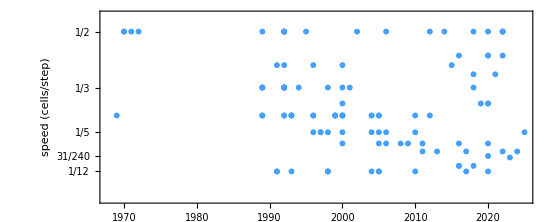

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[8],Opacity[.2],Point[{0,0}]},Style[Text[Style["⟶",Bold,11],{0,0}],GrayLevel[.3]]}],#+Pi/2], 30}&/@as)]]
```

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[8],Opacity[.2],Point[{0,0}]},Style[Text[Style["⟶",Bold,11],{0,0}],GrayLevel[.3]]}],#+Pi/2], 30}&/@as)]]
```

-Graphics-

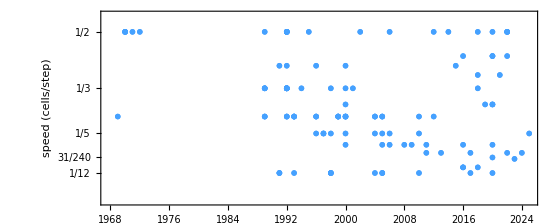

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0,0}]},Style[Text[Style["⟶",Bold,11],{0,0}],GrayLevel[.3]]}],#], 30}&/@as)]]
```

```mathematica
1/7 // Head
```

Rational

```mathematica
1/12 // Head
```

Rational

```mathematica
((√5)/6) [[1]]
```

1/6

```mathematica
ToString[((√5)/6) [[1]] * ((√5)/6) [[2]]]
```

```mathematica
ToString[√5]
```

Sqrt[5]

```mathematica
Plot[x^2,{x,0,10},AxesLabel->{Style["x",14],Style[Sqrt[x],14]}]
```

```mathematica
Style[GraphicsRow[Text/@{"√",n}],14]
```

-Graphics-

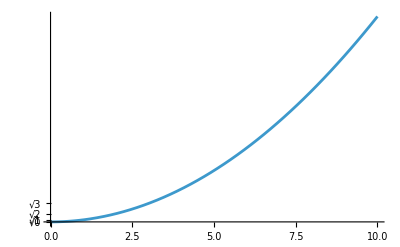

```mathematica
Plot[x^2,{x,0,10},Ticks->{Automatic,Table[{n^2,Style[Row[{"√",n}],14]},{n,0,3}]}]
```

```mathematica
1/ 12
```

```mathematica
{#,If[Head[#] === Times,Text[#], InputForm[#]]}&/@Union[Last/@Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]]
```

{{1/12,1/12},{1/10,1/10},{1/8,1/8},{31/240,31/240},{1/7,1/7},{1/6,1/6},{1/5,1/5},{1/4,1/4},{2/7,2/7},{1/3,1/3},{2/5,2/5},{3/7,3/7},{1/2,1/2},{(√5)/6,(√5)/6}}

```mathematica
DeleteCases[Union[Last/@Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]], x_/; Head[x] ===Times]
```

{1/12,1/10,1/8,31/240,1/7,1/6,1/5,1/4,2/7,1/3,2/5,3/7,1/2}

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,If[Head[#] === Times,Text[#], InputForm[#]]}&/@Delete[DeleteCases[Union[Last/@data], x_/; Head[x] ===Times], 4],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],

FrameTicksStyle->8,PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0, 0}]},Style[Text[Style["⟶",Bold, GrayLevel[.2],9],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&/@as), PlotRangePadding->{{Automatic, .1}, {Automatic, 0}}]]
```

-Graphics-

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{Table[{i/10, Text[ToString[i]<>"/"<>"10"]}, {i, 1, 5}], None}, {Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],
PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0, 0}]},Style[Text[Style["⟶",Bold, GrayLevel[.2],9],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&/@as), PlotRangePadding->{{Automatic, .1}, {Automatic, 0}}, GridLines->{None, Automatic}, GridLinesStyle->Directive[Opacity[.3],Gray, Dashed]]]
```

-Graphics-

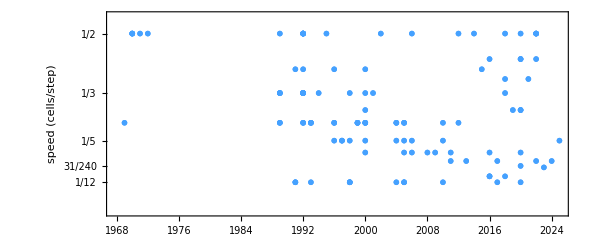

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[{#Year,Norm[#Speed]}& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0, 0}]},Style[Text[Style["⟶",Bold,9],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&/@as)]]
```

#### Ignore

```mathematica
Position[#Name&/@ Catenate[GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&]], "Sir Robin"]
```

{{110}}

```mathematica
Position[#Name&/@ Catenate[GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&]], "Sir robin
```

```mathematica
as[[110]]
```

-ArcTan[1/2]

```mathematica
({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0, 0}]},Style[Text[Style["⟶",Bold,9],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&/@as)[[110]]
```

{-Graphics-,30}

### Clean up

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[BoundingBoxLayeredGraph[#,#Period,ImageSize->{Automatic,140}],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{{2,3,4,5,6,7,8,9,10},{12,15,16,20,21,30,36}},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-period 10  -Graphics-period 12  
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-period 20  
-Graphics-period 21  
-Graphics-
-Graphics-period 30  
-Graphics-period 36

```mathematica
ps = {2,3,4,5,6,7,8,9,10,12,15,16,20,21,30,36};
```

```mathematica
byperiod = SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&MemberQ[ps, #[["Period"]]]&]],#Period&]),#[[1,"Period"]]&];
```

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,#1⟦Period⟧]&].

Values::invrl: The argument Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,#1⟦Period⟧]&] is not a valid Association or a list of rules.

GatherBy::list: List expected at position 1 in GatherBy[Values[Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,Slot[«1»]⟦Period⟧]&]],#Period&].

Function::slot1: (#Year&)[Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,#1⟦Period⟧]&]] is expected to have an Association as the first argument.

Values::invrl: The argument Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,#1⟦Period⟧]&] is not a valid Association or a list of rules.

Function::slot1: (#Year&)[#Period] is expected to have an Association as the first argument.

GatherBy::list: List expected at position 1 in GatherBy[Values[Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,Slot[«1»]⟦Period⟧]&]],#Period&].

Part::pspec1: Part specification Period is not applicable.

GatherBy::list: List expected at position 1 in GatherBy[#Period&,Values[Select[$Failed,#Class===Spaceship&&KeyExistsQ[#1,Period]&&MemberQ[ps,Slot[«1»]⟦Period⟧]&]]].

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[BoundingBoxLayeredGraph[#,#Period,ImageSize->{Automatic,140}],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{{2,3,4,5,6,7,8,9,10},{12,15,16,20,21,30,36}},Spacer[15]]
```